```mathematica
WolframAlpha["integrate 1/(4*Pi*a)*(exp(-(x-s)^2/(2a))+exp(-(x+s)^2/(2a)))^2",{{"IndefiniteIntegral",1},"Output"}]
```

HoldComplete[(2 Erf[x/(√a)]+ⅇ^(s^2/a) (Erf[(-s+x)/(√a)]+Erf[(s+x)/(√a)]))/(8 √a ⅇ^(s^2/a) √π)]

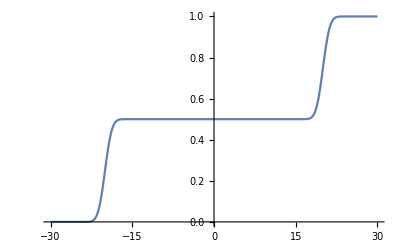

```mathematica
a=2.0;s=20.0;

f[x_]=(2 Erf[x/(√a)]+ⅇ^(s^2/a) (Erf[(-s+x)/(√a)]+Erf[(s+x)/(√a)]))/(8 √a ⅇ^(s^2/a) √π);
g[x_]=1/((f[Infinity]-f[-Infinity]))*(f[x]-f[-Infinity]);
Plot[g[x],{x,-30,30}]
```

```mathematica
f[x_,t_]=(1/(2*Sqrt[Pi*2]*(1+ⅈ*t*1/2))*Exp[-((x-20)^2+(600)^2)/(2*2*(1+ⅈ*t*1/2))+ⅈ*((8*600+32*t)/(1+ⅈ*t*1/2))]+1/(2*Sqrt[Pi*2]*(1+ⅈ*t*1/2))*Exp[-((x+20)^2+(600)^2)/(2*2*(1+ⅈ*t*1/2))+ⅈ*((8*600+32*t)/(1+ⅈ*t*1/2))])*(1/(2*Sqrt[Pi*2]*(1-ⅈ*t*1/2))*Exp[-((x-20)^2+(600)^2)/(2*2*(1-ⅈ*t*1/2))-ⅈ*((8*600+32*t)/(1-ⅈ*t*1/2))]+1/(2*Sqrt[Pi*2]*(1-ⅈ*t*1/2))*Exp[-((x+20)^2+(600)^2)/(2*2*(1-ⅈ*t*1/2))-ⅈ*((8*600+32*t)/(1-ⅈ*t*1/2))]);
g=NIntegrate[f[x,60],{x,-Infinity,Infinity}];
```

```mathematica
Plot[f[x,50],{x,-100,100}]
```

-Graphics-

{{-100.,2.348×10^101},{-99.9,2.37811×10^101},{-99.8,2.41186×10^101},{-99.7,2.44931×10^101},{-99.6,2.49055×10^101},{-99.5,2.53562×10^101},{-99.4,2.58457×10^101},{-99.3,2.63744×10^101},{-99.2,2.69427×10^101},{-99.1,2.75505×10^101},1982,{99.2,2.69427×10^101},{99.3,2.63744×10^101},{99.4,2.58457×10^101},{99.5,2.53562×10^101},{99.6,2.49055×10^101},{99.7,2.44931×10^101},{99.8,2.41186×10^101},{99.9,2.37811×10^101},{100.,2.348×10^101}}
 |  |  |  |

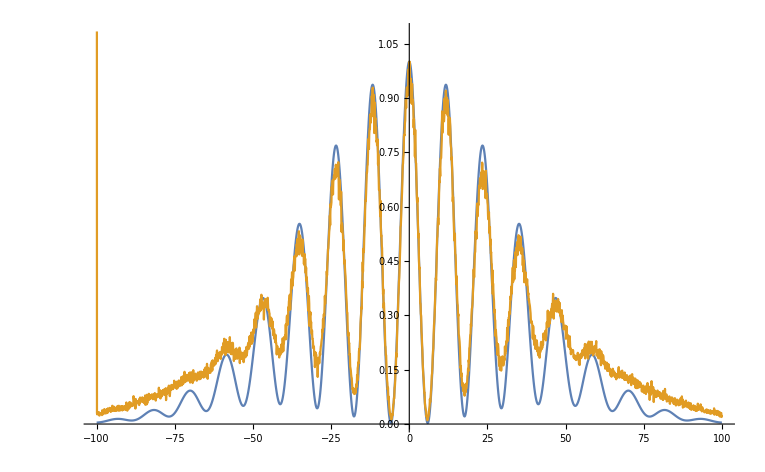

```mathematica
f[x_,t_,a_,s_,k_]=(1/(2*Sqrt[Pi*a]*(1+ⅈ*t*1/a))*Exp[-((x-s)^2+(600)^2)/(2*a*(1+ⅈ*t*1/a))+ⅈ*((k*600+k^2/2*t)/(1+ⅈ*t*1/a))]+1/(2*Sqrt[Pi*a]*(1+ⅈ*t*1/a))*Exp[-((x+s)^2+(600)^2)/(2*a*(1+ⅈ*t*1/a))+ⅈ*((k*600+k^2/2*t)/(1+ⅈ*t*1/a))])*(1/(2*Sqrt[Pi*a]*(1-ⅈ*t*1/a))*Exp[-((x-s)^2+(600)^2)/(2*a*(1-ⅈ*t*1/a))-ⅈ*((k*600+k^2/2*t)/(1-ⅈ*t*1/a))]+1/(2*Sqrt[Pi*a]*(1-ⅈ*t*1/a))*Exp[-((x+s)^2+(600)^2)/(2*a*(1-ⅈ*t*1/a))-ⅈ*((k*600+k^2/2*t)/(1-ⅈ*t*1/a))]);



data=Import["/home/markus/build-nelsonclass-Desktop-Debug/h.txt",{"Data",{All},{1,2}}];
ListPlot[data,Joined->True];




Show[ListPlot[data,Joined->True,Filling->Axis],Plot[f[x,60,2,16,8]*145*10^(-103),{x,-100,100},PlotStyle->Red],PlotRange->All,Ticks->{Automatic,None}];

md=Table[{(n-1001)/10,data[[n,2]]},{n,200,1800,1}];
max=Max[md[[All,2]]];
data2=Table[{(n-1001)/10,data[[n,2]]/max},{n,1,2001,1}];

data3=Table[{n,Re[f[n,60,2,16,8]]},{n,-100,100,0.1}]
max=Max[data3[[All,2]]];
data4=Table[{(n-1001)/10,data3[[n,2]]/max},{n,1,2001,1}];

ListPlot[{data4,data2},Joined->True,Filling->{None,Blue}]
ListPlot[{data4,data2},Joined->True,Filling->{1->{{2},{Red,Red}}}]

ListPlot[data2,Joined->True];
ListPlot[data4,Joined->True];

Plot[f[x,60,2,20,8],{x,-100,100},PlotStyle->Red];
```

```mathematica
Re[f[n,75,2,20,8]]
```

```mathematica
Max[data[[All,2]]]
data[[100,2]]/Max[data[[All,2]]]
```

3590

33/3590

```mathematica
data2=Table[{(n-1001)/10,data[[n,2]]/max},{n,1,2001,1}]
ListPlot[data2,Joined->True]
```

3590

{{-100,1},{-999/10,21/3590},{-499/5,12/1795},{-997/10,23/3590},{-498/5,12/1795},{-199/2,9/1795},{-497/5,13/1795},{-993/10,3/359},{-496/5,11/1795},{-991/10,21/3590},{-99,11/1795},1980,{991/10,7/1795},{496/5,6/1795},{993/10,5/718},{497/5,8/1795},{199/2,9/1795},{498/5,12/1795},{997/10,23/3590},{499/5,2/359},{999/10,17/3590},{100,23/3590}}
 |  |  |  |

0.0263974

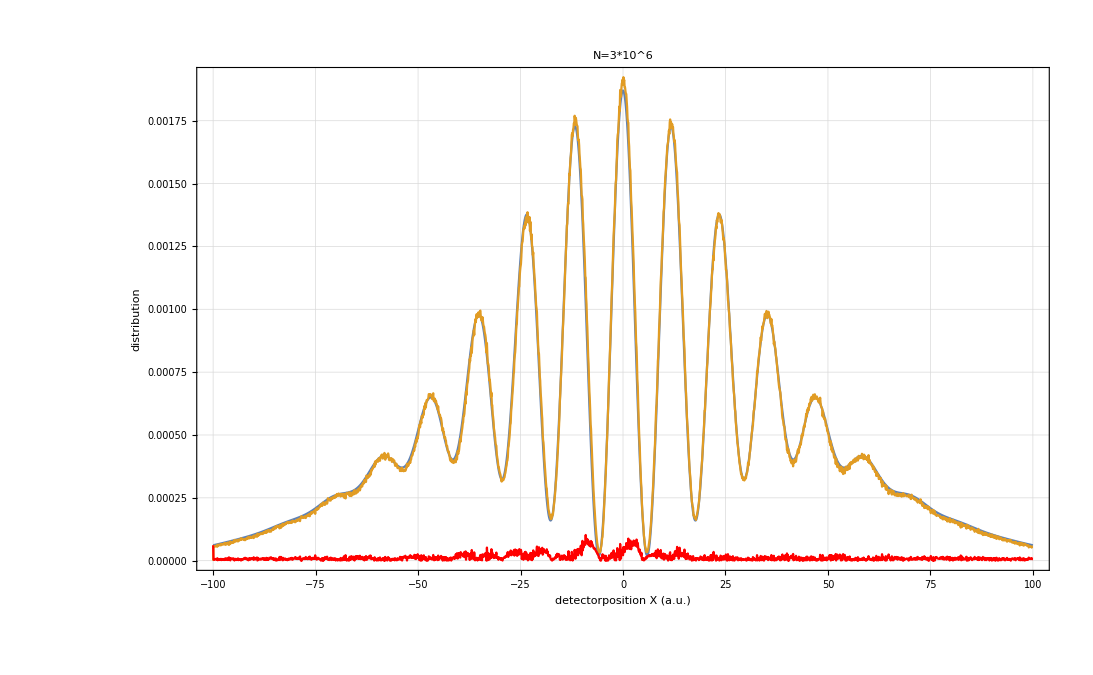

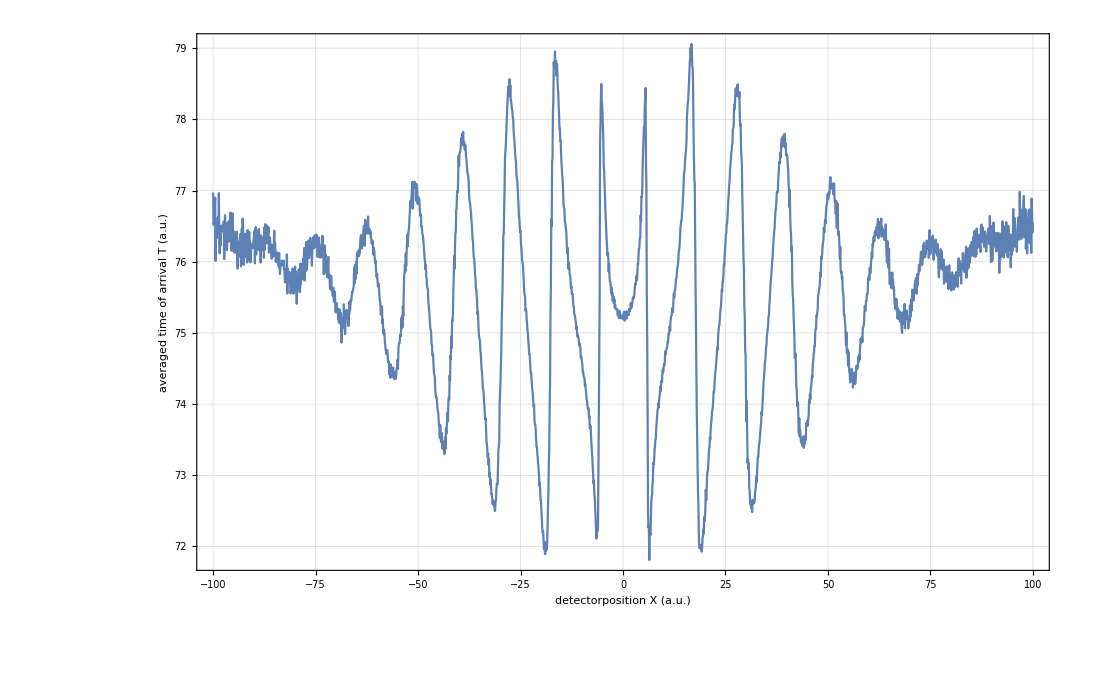

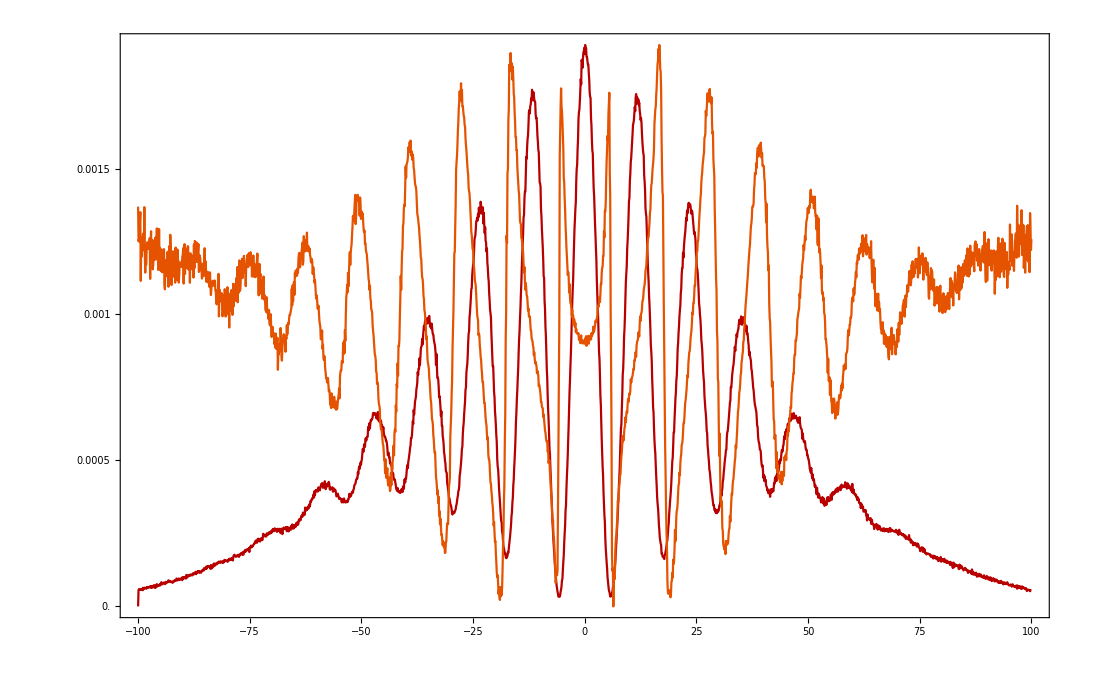

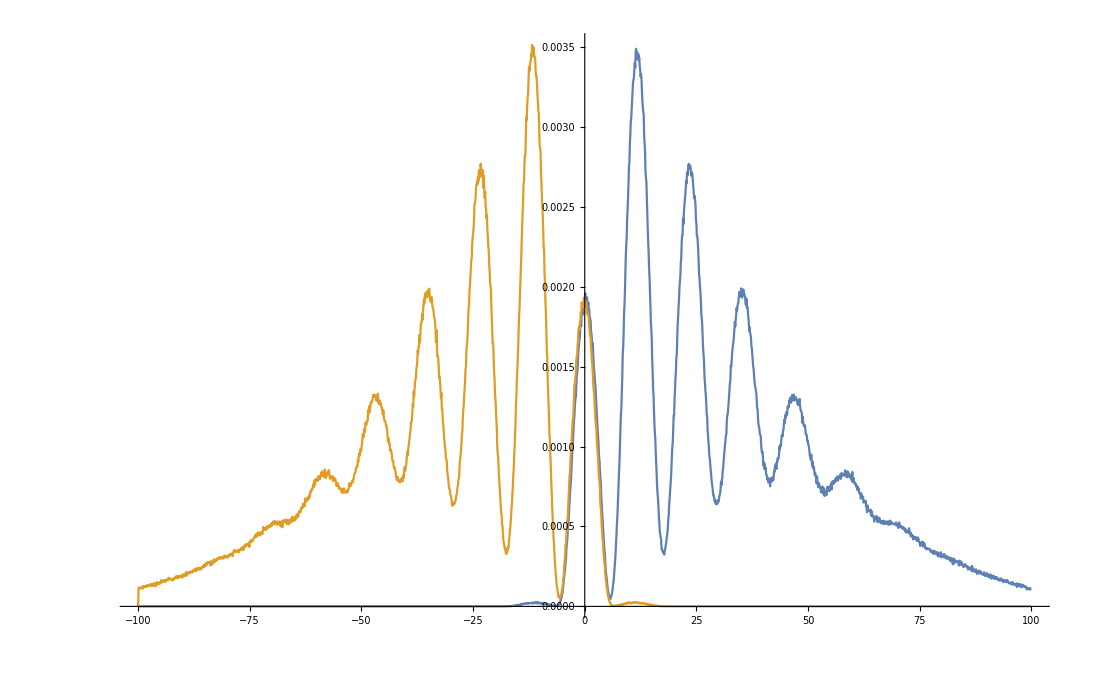

```mathematica
f[x_,t_,a_,s_,k_]=(1/(2*Sqrt[Pi*a]*(1+ⅈ*t*1/a))*Exp[-((x-s)^2+(600)^2)/(2*a*(1+ⅈ*t*1/a))+ⅈ*((k*600+k^2/2*t)/(1+ⅈ*t*1/a))]+1/(2*Sqrt[Pi*a]*(1+ⅈ*t*1/a))*Exp[-((x+s)^2+(600)^2)/(2*a*(1+ⅈ*t*1/a))+ⅈ*((k*600+k^2/2*t)/(1+ⅈ*t*1/a))])*(1/(2*Sqrt[Pi*a]*(1-ⅈ*t*1/a))*Exp[-((x-s)^2+(600)^2)/(2*a*(1-ⅈ*t*1/a))-ⅈ*((k*600+k^2/2*t)/(1-ⅈ*t*1/a))]+1/(2*Sqrt[Pi*a]*(1-ⅈ*t*1/a))*Exp[-((x+s)^2+(600)^2)/(2*a*(1-ⅈ*t*1/a))-ⅈ*((k*600+k^2/2*t)/(1-ⅈ*t*1/a))]);

g[x_,t_,a_,s_,k_]=Sum[Re[f[x,y,a,s,k]],{y,0,100,1}];

data=Import["/home/markus/build-nelsonclass-Desktop-Release/h.txt",{"Data",{All},{1,2}}];
ListPlot[data,Joined->True];
data[[1,2]]=0;
md=Table[{(n-1001)/10,data[[n,2]]},{n,1,2001,1}];
max=Sum[md[[n,2]],{n,1,2001}];
data2=Table[{(n-1001)/10,data[[n,2]]/max},{n,1,2001,1}];

data3=Table[{n,Re[g[n,75,2,20,8]]},{n,-100,100,0.1}];
max=Sum[data3[[n,2]],{n,1,2001}];
data4=Table[{(n-1001)/10,data3[[n,2]]/max},{n,1,2001,1}];
error=Table[{(n-1001)/10,Abs[(data4[[n,2]]-data2[[n,2]])]},{n,1,2001,1}];
Sum[Abs[(data4[[n,2]]-data2[[n,2]])],{n,2,2001}]

ListPlot[{data4,data2,error},Joined->True,PlotLabel->"N=3*10^6",PlotStyle->{,,Red},Filling->{None,Blue,Red},PlotRange->All,PlotTheme->"Detailed", FrameLabel->{"detectorposition X (a.u.)","distribution"}]


data=Import["/home/markus/build-nelsonclass-Desktop-Release/h.txt",{"Data",{All},{1,3}}];
ListPlot[data,Joined->True,PlotTheme->"Detailed", FrameLabel->{"detectorposition X (a.u.)","averaged time of arrival T (a.u.)"}]


TwoAxisListPlot[{f_,g_},opts___]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[ListPlot[#,Axes->True,PlotStyle->ColorData[85][#2[[1]]],opts]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};
fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]

TwoAxisListPlot[{data2,data},Joined->True]


datal=Import["/home/markus/build-nelsonclass-Desktop-Release/h.txt",{"Data",{All},{1,4}}];
datal[[1,2]]=0;
md=Table[{(n-1001)/10,datal[[n,2]]},{n,1,2001,1}];
max=Sum[md[[n,2]],{n,1,2001}];
datall=Table[{(n-1001)/10,datal[[n,2]]/max},{n,1,2001,1}];

datar=Import["/home/markus/build-nelsonclass-Desktop-Release/h.txt",{"Data",{All},{1,5}}];
md=Table[{(n-1001)/10,datar[[n,2]]},{n,1,2001,1}];
max=Sum[md[[n,2]],{n,1,2001}];
datarr=Table[{(n-1001)/10,datar[[n,2]]/max},{n,1,2001,1}];


ListPlot[{datarr,datall},Joined->True,PlotRange->All]
```

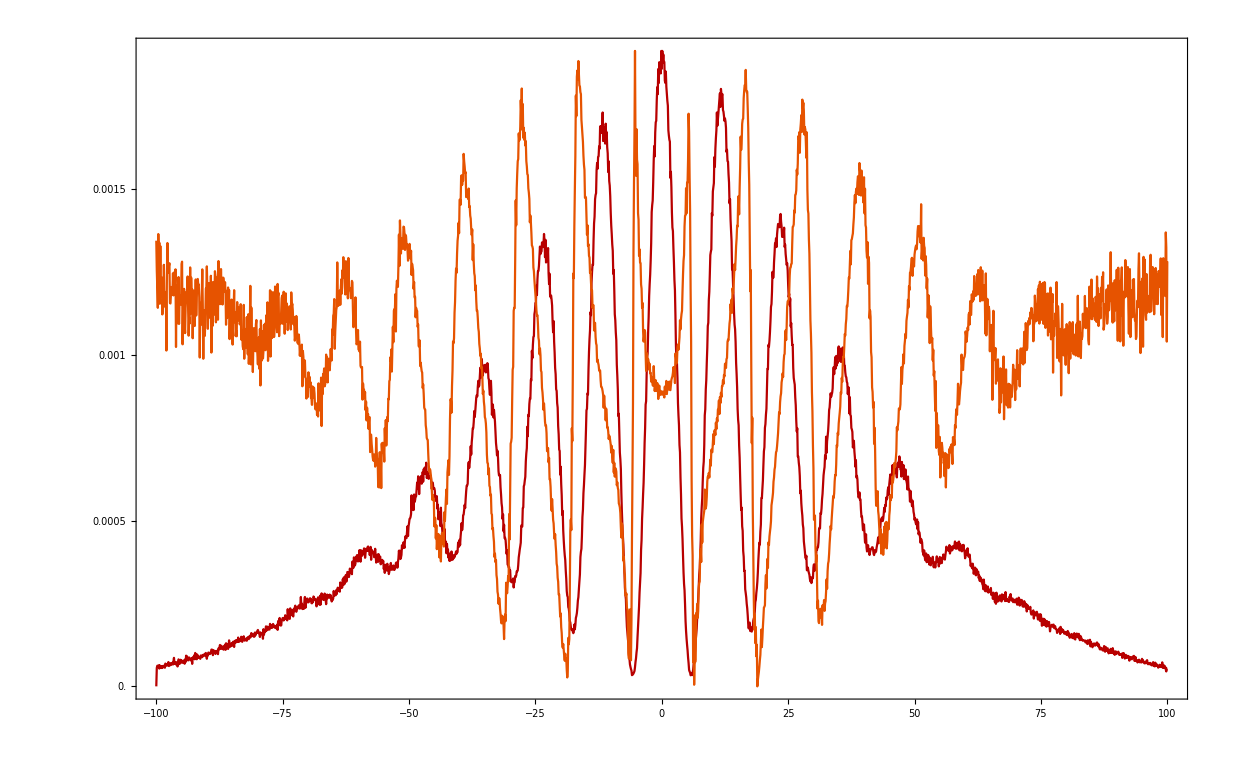

$Aborted

0.0345271

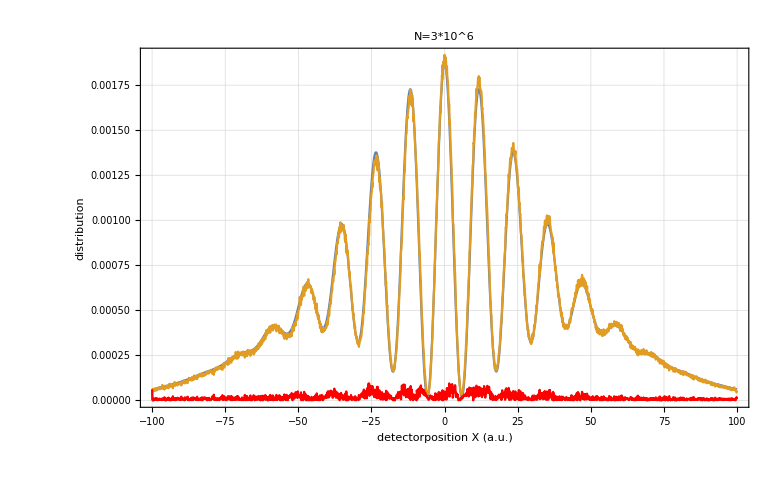

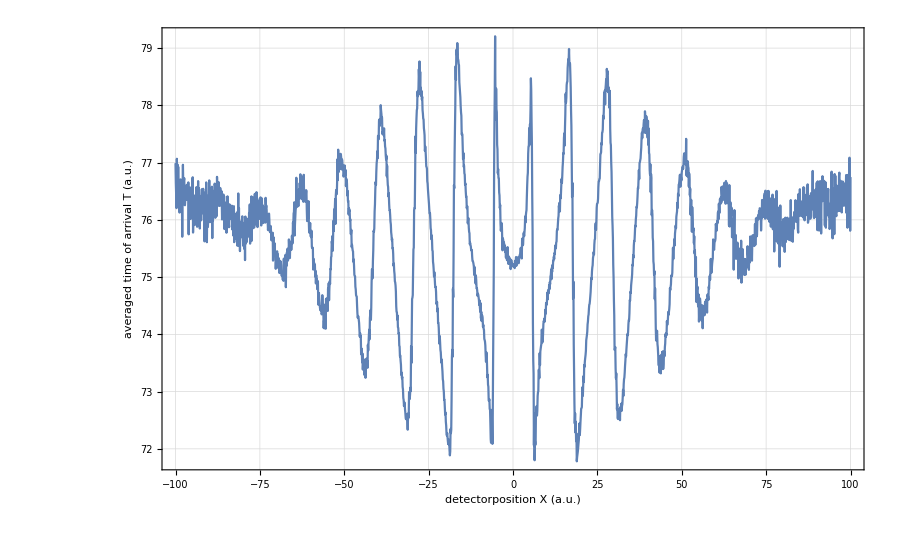

```mathematica
f[x_,t_,a_,s_,k_]=(1/(2*Sqrt[Pi*a]*(1+ⅈ*t*1/a))*Exp[-((x-s)^2+(600)^2)/(2*a*(1+ⅈ*t*1/a))+ⅈ*((k*600+k^2/2*t)/(1+ⅈ*t*1/a))]+1/(2*Sqrt[Pi*a]*(1+ⅈ*t*1/a))*Exp[-((x+s)^2+(600)^2)/(2*a*(1+ⅈ*t*1/a))+ⅈ*((k*600+k^2/2*t)/(1+ⅈ*t*1/a))])*(1/(2*Sqrt[Pi*a]*(1-ⅈ*t*1/a))*Exp[-((x-s)^2+(600)^2)/(2*a*(1-ⅈ*t*1/a))-ⅈ*((k*600+k^2/2*t)/(1-ⅈ*t*1/a))]+1/(2*Sqrt[Pi*a]*(1-ⅈ*t*1/a))*Exp[-((x+s)^2+(600)^2)/(2*a*(1-ⅈ*t*1/a))-ⅈ*((k*600+k^2/2*t)/(1-ⅈ*t*1/a))]);

g[x_,t_,a_,s_,k_]=Integrate[Re[f[x,y,a,s,k]],{y,1,100}];

data=Import["/home/markus/build-nelsonclass-Desktop-Release/h.txt",{"Data",{All},{1,2}}];
ListPlot[data,Joined->True];
data[[1,2]]=0;
md=Table[{(n-1001)/10,data[[n,2]]},{n,1,2001,1}];
max=Sum[md[[n,2]],{n,1,2001}];
data2=Table[{(n-1001)/10,data[[n,2]]/max},{n,1,2001,1}];

data3=Table[{n,Re[g[n,75,2,20,8]]},{n,-100,100,0.1}];
max=Sum[data3[[n,2]],{n,1,2001}];
data4=Table[{(n-1001)/10,data3[[n,2]]/max},{n,1,2001,1}];
error=Table[{(n-1001)/10,Abs[(data4[[n,2]]-data2[[n,2]])]},{n,1,2001,1}];
Sum[Abs[(data4[[n,2]]-data2[[n,2]])],{n,2,2001}]

ListPlot[{data4,data2,error},Joined->True,PlotLabel->"N=3*10^6",PlotStyle->{,,Red},Filling->{None,Blue,Red},PlotRange->All,PlotTheme->"Detailed", FrameLabel->{"detectorposition X (a.u.)","distribution"}]

data=Import["/home/markus/build-nelsonclass-Desktop-Release/h.txt",{"Data",{All},{1,3}}];
ListPlot[data,Joined->True,PlotTheme->"Detailed", FrameLabel->{"detectorposition X (a.u.)","averaged time of arrival T (a.u.)"}]

ListPlot[{data4,data2},Joined->True,Filling->{1->{{2},{Green,Green}}}];
```